## The model

```mathematica
w[x_,xn_,n_]:=re[x,xn,n]/(1+th re[x,xn,n]);
(*re[x_,xn_,n_]:=rb/n(1-(x c1+x^2 c2)+b(((x+(n-1)xn)(1-p)t)/n)^γ-d(1-x)(((x+(n-1)xn)t)/n p)^η);*)
re[x_,xn_,n_]:=rb/n(1-(x C1+x^2 C2)+Bb((x+(n-1)xn)(1-p))^γ/n-Pp(1-x)((x+(n-1)xn)/n p)^η);
```

## Well-mixed population

```mathematica
(w[x,xn,n]/.{xn->y,x->y,γ->1})//FullSimplify
```

1/(th-n/(rb (-1+C1 y+Bb (-1+p) y+C2 y^2-Pp (-1+y) (p y)^η)))

```mathematica
neqwm=Solve[((w[x,xn,n]/.{xn->y,x->y,γ->1})//FullSimplify)==1,n]//FullSimplify
```

{{n→rb (-1+th) (-1+C1 y+Bb (-1+p) y+C2 y^2-Pp (-1+y) (p y)^η)}}

```mathematica
(n/.neqwm[[1]]/.pars/.th->competitionStrength[[#]]//Simplify)&/@Range[3]
```

{8.+17.92 y+0.48 y^2,9.+20.16 y+0.54 y^2,5.+11.2 y+0.3 y^2}

```mathematica
(n/.neqwm[[1]]/.pars/.th->#//Simplify)&/@{0.2,0.1,0.05}
```

{8.+17.92 y+0.48 y^2,9.+20.16 y+0.54 y^2,9.5+21.28 y+0.57 y^2}

-0.6 (-1.+th) (16.6667+37.3333 y+1. y^2)

```mathematica
n/.neqwm[[1]]/.pars
```

-9. (-1-1.6 y+C1 y-0.06 (-1+y) y+C2 y^2)

```mathematica
n/.neqwm[[1]]
```

rb (-1+th) (-1+C1 y+Bb (-1+p) y+C2 y^2-Pp (-1+y) (p y)^η)

```mathematica
D[w[x,xn,n],x]//.{x->y,xn->y,γ->1}//.{neqwm[[1]]}//FullSimplify
```

{-(Pp^2 rb (-1+th) (-1+y) y (p y)^(2 η)+rb (-1+th) y (C1+2 C2 y) (-1+y (C1+C2 y))+Bb (-1+p) y (1+rb (-1+th) y (C1+2 C2 y-Pp (p y)^η))-Pp (p y)^η (rb (-1+th) y (-1+C1 (-1+2 y)+C2 y (-2+3 y))+(-1+y) η))/(rb y (-1+C1 y+Bb (-1+p) y+C2 y^2-Pp (-1+y) (p y)^η)^2)}

```mathematica
D[w[x,xn,n],x]//.{x->y,xn->y,γ->1}//.{neqwm[[1]]}//Simplify
```

{-((2 C2 rb y^2+C1^2 rb (-1+th) y^2-2 C2 rb th y^2-2 C2^2 rb y^4+2 C2^2 rb th y^4-Pp rb y (p y)^η+Pp rb th y (p y)^η-2 C2 Pp rb y^2 (p y)^η+2 C2 Pp rb th y^2 (p y)^η+3 C2 Pp rb y^3 (p y)^η-3 C2 Pp rb th y^3 (p y)^η+Pp^2 rb y (p y)^(2 η)-Pp^2 rb th y (p y)^(2 η)-Pp^2 rb y^2 (p y)^(2 η)+Pp^2 rb th y^2 (p y)^(2 η)+Bb (-1+p) y (1+C1 rb (-1+th) y+2 C2 rb (-1+th) y^2+Pp rb y (p y)^η-Pp rb th y (p y)^η)+C1 rb (-1+th) y (-1+3 C2 y^2-Pp (p y)^η (-1+2 y))+Pp (p y)^η η-Pp y (p y)^η η)/(rb y (-1+C1 y+Bb (-1+p) y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2))}

```mathematica
s=-(Pp^2 rb (-1+th) (-1+y) y (p y)^(2 η)+rb (-1+th) y (C1+2 C2 y) (-1+y (C1+C2 y))+Bb (-1+p) y (1+rb (-1+th) y (C1+2 C2 y-Pp (p y)^η))-Pp (p y)^η (rb (-1+th) y (-1+C1 (-1+2 y)+C2 y (-2+3 y))+(-1+y) η))/(rb y (-1+C1 y+Bb (-1+p) y+C2 y^2-Pp (-1+y) (p y)^η)^2);
```

### Figure one mid-thesis

```mathematica
competitionStrength={0.2,0.1,0.5};
competitionColours={Black,Gray,LightGray}
```

{GrayLevel[0],GrayLevel[0.5],GrayLevel[0.85]}

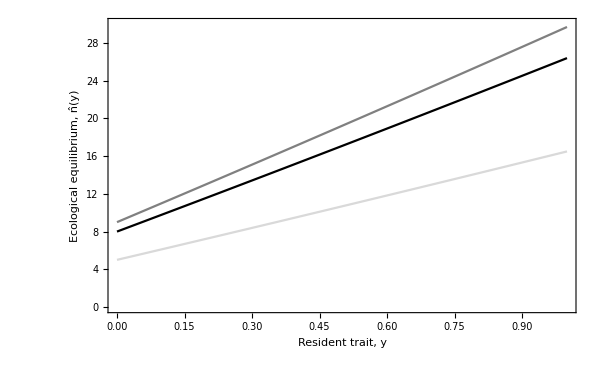

```mathematica
pars={rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0};
Show[Plot[n/.neqwm[[1]]/.pars/.th->competitionStrength[[#]]//Simplify,{y,0,1},PlotStyle->competitionColours[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,30}}]&/@Range[3]]
```

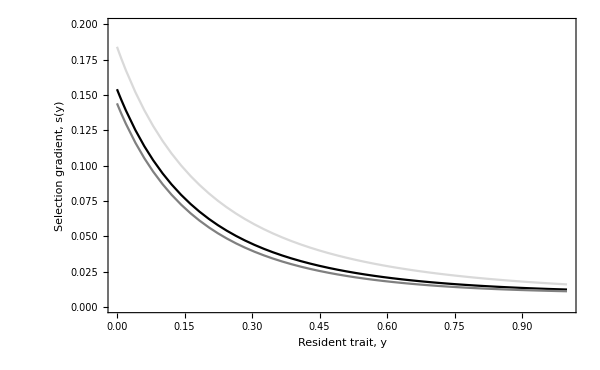

```mathematica
Show[Plot[s/.pars/.th->competitionStrength[[#]],{y,0,1},ImageSize->600,PlotStyle->competitionColours[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},{0,0.2}}]&/@Range[3]]
```

### Figure two mid-thesis

```mathematica
rbLevels={5,10,15};
BbLevels={1,2,3};
PpLevels={0.5,2,5};
pLevels={0.1,0.5,0.9};
γLevels={0.5,1,2};
ηLevels={0.5,1,2};
C1Levels={0.1,1,2};
C2Levels={0,1,2};
mylgds={"low        ", "intermediate        ", "high           "};
mycols={LightGray,Gray,Black}
```

{GrayLevel[0.85],GrayLevel[0.5],GrayLevel[0]}

```mathematica
(*{rb->10,th->0.1,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0}*)
```

#### Effect of baseline resources on n and y

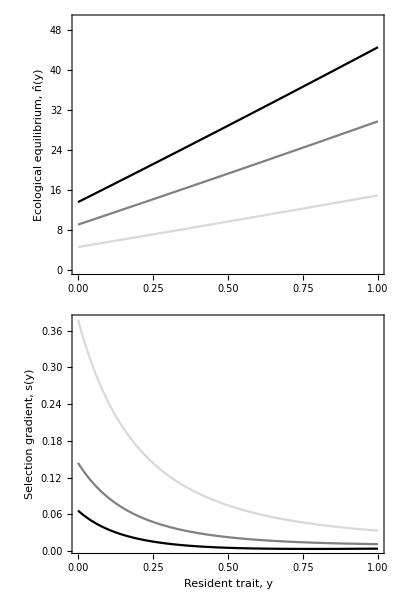

```mathematica
rbfig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->rbLevels[[#]],Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->rbLevels[[#]],Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["r_b=",ToString[rbLevels[[#]]]],15],None,None},{0.9,0.8}]]&/@Range[3]]},Spacings->0]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedrb.pdf",rbfig]
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedrb.pdf

#### Effect of benefit on s and n

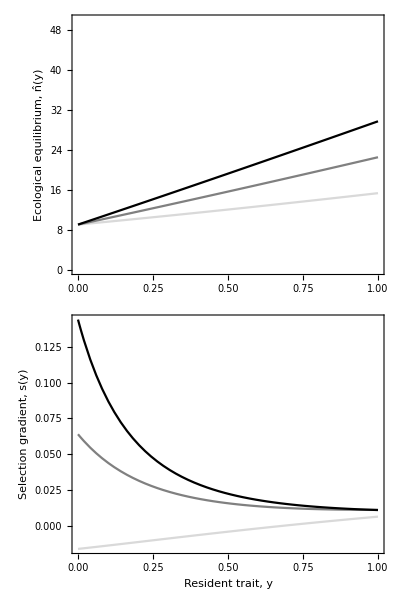

```mathematica
bfig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->BbLevels[[#]],Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->BbLevels[[#]],Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["b=",ToString[BbLevels[[#]]]],15],None,None},{0.9,0.8}]]&/@Range[3]]},Spacings->0]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedb.pdf",bfig]
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedb.pdf

#### Effect of policing cost on s and n

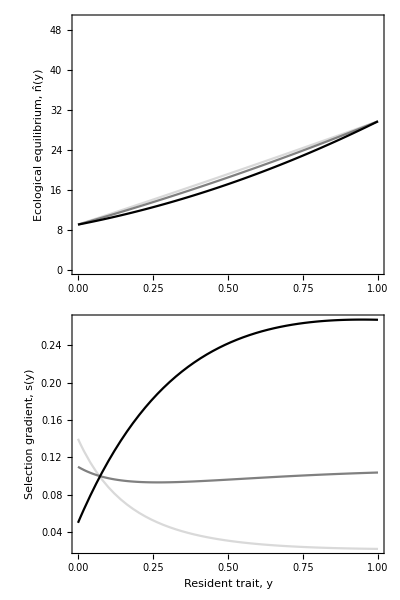

```mathematica
dfig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->3,Pp->PpLevels[[#]],p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->3,Pp->PpLevels[[#]],p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["d=",ToString[PpLevels[[#]]]],15],None,None},{0.9,0.8}]]&/@Range[3]]},Spacings->0]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedd.pdf",dfig]
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedd.pdf

#### Effect of policing proportion on s and n

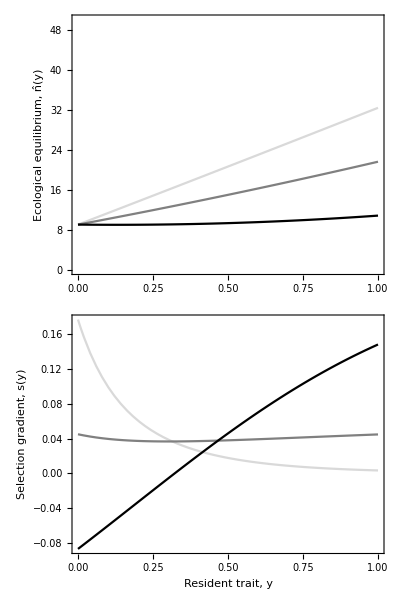

```mathematica
pfig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->3,Pp->0.3,p->pLevels[[#]],γ->1,η->1,C1->0.1,C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->3,Pp->0.3,p->pLevels[[#]],γ->1,η->1,C1->0.1,C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["p=",ToString[pLevels[[#]]]],15],None,None},{0.9,0.2}]]&/@Range[3]]},Spacings->0]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedp.pdf",pfig]
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedp.pdf

#### Effect of benefit modulator on s and n

```mathematica
(*There is no effect: all lines overlap *)
```

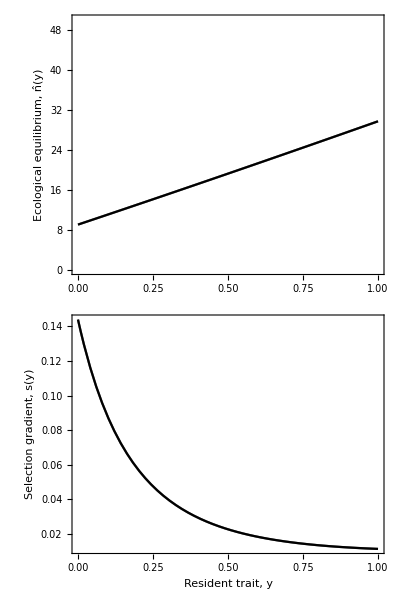

```mathematica
γfig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->γLevels[[#]],η->1,C1->0.1,C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->γLevels[[#]],η->1,C1->0.1,C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["γ=",ToString[γLevels[[#]]]],15],None,None},{0.9,0.2}]]&/@Range[3]]},Spacings->0]
```

```mathematica
(*Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedgamma.pdf",γfig]*)
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedp.pdf

#### Effect of cost modulator on s and n

```mathematica
(*There is no effect: all lines overlap *)
```

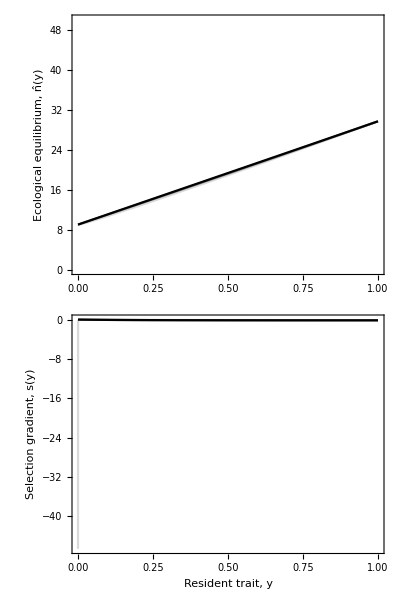

```mathematica
ηfig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->ηLevels[[#]],C1->0.1,C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->ηLevels[[#]],C1->0.1,C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["η=",ToString[ηLevels[[#]]]],15],None,None},{0.9,0.2}]]&/@Range[3]]},Spacings->0]
```

```mathematica
(*Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedeta.pdf",ηfig]*)
```

#### Effect of linear investment cost on s and n

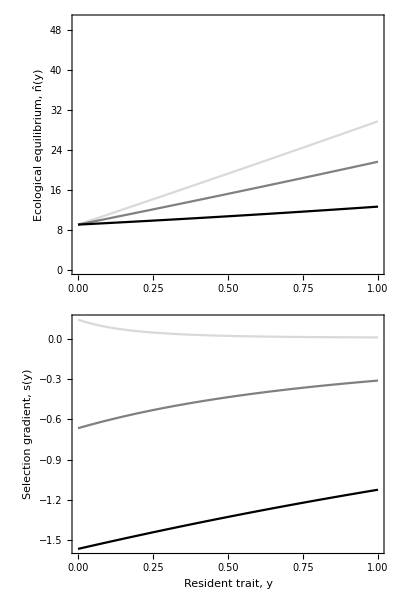

```mathematica
c1fig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->C1Levels[[#]],C2->0,th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->C1Levels[[#]],C2->0,th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["c_1=",ToString[C1Levels[[#]]]],15],None,None},{0.9,0.5}]]&/@Range[3]]},Spacings->0]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedc1.pdf",c1fig]
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedc1.pdf

#### Effect of quadratic investment cost on s and n

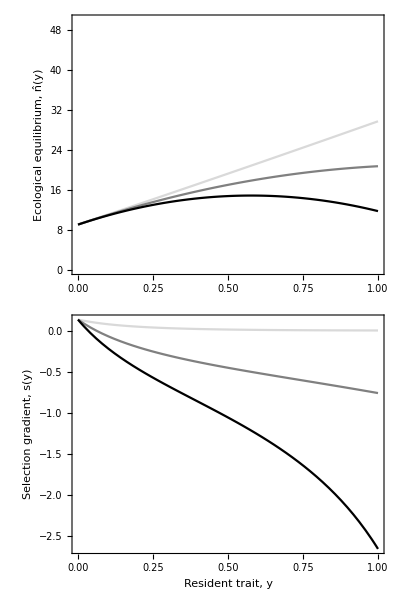

```mathematica
c2fig=Column[{Show[Plot[n/.neqwm[[1]]/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->C2Levels[[#]],th->0.1}//Simplify,{y,0,1},PlotStyle->mycols[[#]],Frame->True,FrameLabel->{None,Style["Ecological equilibrium, n̂(y)",20]}, ImageSize->600,PlotRange->{{0,1},{0,50}}]&/@Range[3]],Show[Plot[s/.{rb->10,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->C2Levels[[#]],th->0.1},{y,0,1},ImageSize->600,PlotStyle->mycols[[#]],Frame->True,FrameLabel->{Style["Resident trait, y",20],Style["Selection gradient, s(y)",20]},PlotRange->{{0,1},All},PlotLegends->Placed[{Style[StringJoin["c_2=",ToString[C2Levels[[#]]]],15],None,None},{0.9,0.5}]]&/@Range[3]]},Spacings->0]
```

```mathematica
Export["/home/claire/Dropbox/PhD/Results/figs/snwellmixedc2.pdf",c2fig]
```

/home/claire/Dropbox/PhD/Results/figs/snwellmixedc2.pdf

```mathematica
Select[Chop[#[[1]]]&/@NSolve[(s/.pars/.{rb->15,Bb->3,Pp->0.3,p->0.2,γ->1,η->1,C1->0.1,C2->0,th->0.1}//FullSimplify)==0,y],0<y<1]
```

{}

### Find evolutionary equilibria

```mathematica
Solve[(s/.neqwm[[1]])==0,y]
```

$Aborted

```mathematica
anasolve=Solve[(s/.η->1)==0,y]
```

1
 |  |  |  |

```mathematica
Length[%]
```

3

```mathematica
y/.anasolve/.pars (*complex numbers, or negligible imaginary part?*)
```

{39.0891+1.11022×10^-16 ⅈ,-1.22646+1.77636×10^-15 ⅈ,0.637352-1.77636×10^-15 ⅈ}

```mathematica
Chop[#]&/@NSolve[(s/.pars)==0]
```

{{y→-36.8842},{y→0.608779-0.913433 ⅈ},{y→0.608779+0.913433 ⅈ}}

```mathematica
0.6087789019316929-0.9134330234898707 ⅈ//Chop
```

0.608779-0.913433 ⅈ

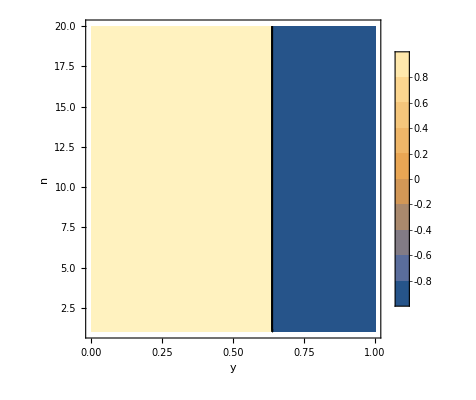

```mathematica
pars={th -> 0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,p->0.2,γ->1,η->1};
ContourPlot[Sign[(s/.pars)],{y,0,1-10^-6},{n,1,20},PlotLegends->Automatic,Frame->True,FrameLabel->{Style["y",20],Style["n",20],Style["selection gradient",20]},MaxRecursion->3]
```

## Structured population

### Selection gradient

```mathematica
w[x_,xn_,n_]:=re[x,xn,n]/(1+th re[x,xn,n]);
re[x_,xn_,n_]:=rb/n(1-(x C1+x^2 C2)+Bb((x+(n-1)xn)(1-p))^γ/n-Pp(1-x)((x+(n-1)xn)/n p)^η);
```

```mathematica
F[xm_,n_,nr_]:=(1-m)w[xm,xm,n]n+m nr
```

```mathematica
monopop={x->y,xn->y,xm->y,nr->n,r->(1-m)^2/(1+(1-(1-m)^2)(n-1)),r̄->1/n+(1-1/n)r};
```

```mathematica
sw=D[w[x,xn,n],x]+D[w[x,xn,n],xn]*r//.monopop//Simplify
```

-(n^2 rb (C1 (-1-2 m (-1+n)+m^2 (-1+n)) n y+2 C2 (-1-2 m (-1+n)+m^2 (-1+n)) n y^2+n Pp y (p y)^η-2 m n Pp y (p y)^η+m^2 n Pp y (p y)^η+2 m n^2 Pp y (p y)^η-m^2 n^2 Pp y (p y)^η+Bb (-n (-1+p) y)^γ γ-n Pp (p y)^η η+n Pp y (p y)^η η))/((-1-2 m (-1+n)+m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)

```mathematica
dn=D[F[xm,n,nr],xm]*(1-(1-m)D[F[xm,n,nr],n])^-1*(1-m)r̄//.monopop//Simplify
```

((1-m) (-1+m) n^3 rb (C1 n y+2 C2 n y^2-n Pp y (p y)^η-Bb (-n (-1+p) y)^γ γ+n Pp (p y)^η η-n Pp y (p y)^η η))/((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2 (1-((-1+m)^2 rb (Bb^2 rb th (-n (-1+p) y)^(2 γ)-2 Bb n rb th (-n (-1+p) y)^γ (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+n^2 (rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2+Bb (-n (-1+p) y)^γ (-1+γ))))/((n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)))

```mathematica
se=dn*D[w[x,xn,n],n]//.monopop//Simplify
```

((1-m) (-1+m) n^4 rb^2 (n (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+Bb (-n (-1+p) y)^γ (-2+γ)) (C1 n y+2 C2 n y^2-n Pp y (p y)^η-Bb (-n (-1+p) y)^γ γ+n Pp (p y)^η η-n Pp y (p y)^η η))/((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^4 (1-((-1+m)^2 rb (Bb^2 rb th (-n (-1+p) y)^(2 γ)-2 Bb n rb th (-n (-1+p) y)^γ (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+n^2 (rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2+Bb (-n (-1+p) y)^γ (-1+γ))))/((n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)))

```mathematica
s=sw+se
```

((1-m) (-1+m) n^4 rb^2 (n (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+Bb (-n (-1+p) y)^γ (-2+γ)) (C1 n y+2 C2 n y^2-n Pp y (p y)^η-Bb (-n (-1+p) y)^γ γ+n Pp (p y)^η η-n Pp y (p y)^η η))/((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^4 (1-((-1+m)^2 rb (Bb^2 rb th (-n (-1+p) y)^(2 γ)-2 Bb n rb th (-n (-1+p) y)^γ (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+n^2 (rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2+Bb (-n (-1+p) y)^γ (-1+γ))))/((n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)))-(n^2 rb (C1 (-1-2 m (-1+n)+m^2 (-1+n)) n y+2 C2 (-1-2 m (-1+n)+m^2 (-1+n)) n y^2+n Pp y (p y)^η-2 m n Pp y (p y)^η+m^2 n Pp y (p y)^η+2 m n^2 Pp y (p y)^η-m^2 n^2 Pp y (p y)^η+Bb (-n (-1+p) y)^γ γ-n Pp (p y)^η η+n Pp y (p y)^η η))/((-1-2 m (-1+n)+m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)

### Exploring selection gradient behaviour

```mathematica
pars={th -> 0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,p->0.2,γ->1,η->1};
```

{th→0.1,rb→10,Cc→0.1,Bb→2,Pp→0.3,p→0.2,γ→1,η→1}

```mathematica
eq1=F[xm,n,nr]/.monopop/.pars/.m->0.5//Simplify
```

(n (5.5+0.5 n+8.47 y-0.22 y^2))/(1.+n+1.54 y-0.04 y^2)

```mathematica
eq2=s/.pars/.m->0.5//Simplify
```

(n (-30.8-95.364 y-1.4 n^3 y-72.1213 y^2+2.64876 y^3+0.01232 y^4-0.0008 y^5+n^2 (20.5333-2.46667 y-4.312 y^2+0.112 y^3)+n (-10.2667-10.3773 y+12.012 y^2+4.67903 y^3-0.25872 y^4+0.00336 y^5)))/((0.333333+1. n) (1.+n+1.54 y-0.04 y^2)^2 (-1.5+n^2-4.62 y-3.4374 y^2+0.1848 y^3-0.0024 y^4+n (2.+3.08 y-0.08 y^2)))

```mathematica
FindRoot[{eq1==n,eq2==0},{{n,10,1,30},{y,0.5,0,1}}]
```

{n→17.8282,y→0.64786}

```mathematica
(*simulation results*)
```

```mathematica
demog=Flatten[Import["/home/claire/Dropbox/PhD/Src/test-new-model-results-sim/outputtestdemog.txt_demography.txt","Data"]];
pheno=Flatten[Import["/home/claire/Dropbox/PhD/Src/test-new-model-results-sim/outputtestdemog.txt_phenotypes.txt","Data"]];
```

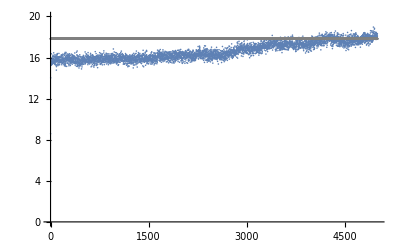

```mathematica
Show[ListPlot[demog,PlotRange->{0,20}],ListPlot[17.828244548000608&/@demog,PlotStyle->Gray]]
```

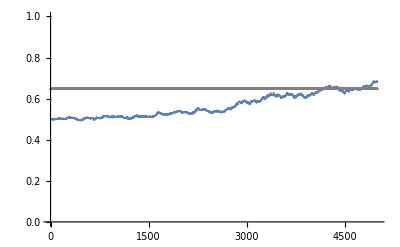

```mathematica
Show[ListPlot[pheno,PlotRange->{0,1}],ListPlot[0.6478603790376822&/@demog,PlotStyle->Gray]]
```

```mathematica
rates=Range[0,1,0.1];
res=Table[FindRoot[{(F[xm,n,nr]/.monopop/.pars/.m->rates[[i]])==n,(s/.pars/.m->rates[[i]]//Simplify)==0},{{n,10,1,30},{y,0.5,0,1}}],{i,Length[rates]}]
```

{{n→9.75264,y→0.0543798},{n→18.1643,y→0.67297},{n→4.43157,y→0.},{n→17.9686,y→0.658344},{n→17.8919,y→0.652616},{n→17.8282,y→0.64786},{n→17.7769,y→0.64403},{n→17.7375,y→0.641088},{n→17.7096,y→0.639007},{n→17.693,y→0.637765},{n→10.0698,y→1.}}

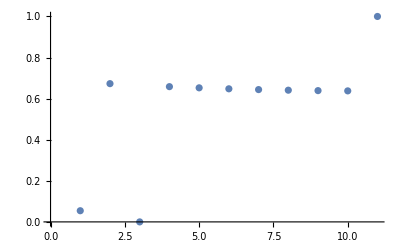

```mathematica
ListPlot[y/.res]
```

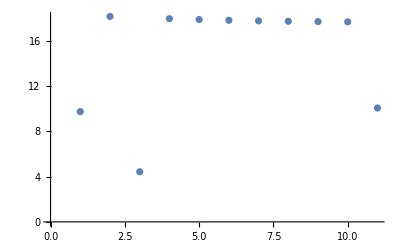

```mathematica
ListPlot[n/.res]
```

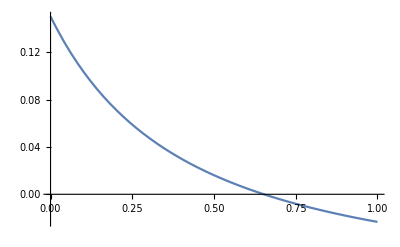

```mathematica
Plot[s/.pars/.m->rates[[5]]/. NSolve[(F[xm,n,nr]/.monopop/.pars/.m->rates[[5]])==n,n]//Simplify,{y,0,1}]
```

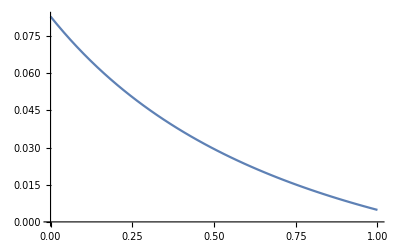

```mathematica
pars2={th->0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,p->0.5,γ->1,η->1};
Plot[s/.pars2/.m->rates[[5]]/. NSolve[(F[xm,n,nr]/.monopop/.pars2/.m->rates[[5]])==n,n]//Simplify,{y,0,1}]
```

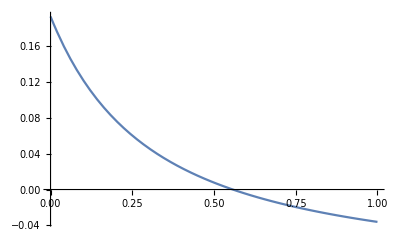

```mathematica
pars3={th->0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,p->0.01,γ->1,η->1};
Plot[s/.pars3/.m->rates[[5]]/. NSolve[(F[xm,n,nr]/.monopop/.pars3/.m->rates[[5]])==n,n]//Simplify,{y,0,1}]
```

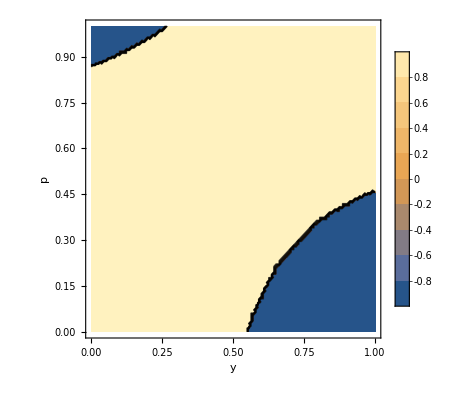

```mathematica
pars={th -> 0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,γ->1,η->1,m->0.5};
ContourPlot[Sign[s/.pars/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars,n]],n->0.]],{y,0,1},{p,0,1},PlotLegends-> Automatic,Frame->True,FrameLabel->{Style["y",20],Style["p",20],Style["selection gradient",20]},ImageSize->400]
```

```mathematica
D[re[x,x,n],x]/.{γ->1,η->1}//Simplify
```

-(rb (Bb (-1+p)+2 Cc x+p (Pp-2 Pp x)))/n

```mathematica
Solve[-(rb (Bb (-1+p)+2 Cc x+p (Pp-2 Pp x)))/n==0,x]
```

{{x→-(-Bb+Bb p+p Pp)/(2 (Cc-p Pp))}}

```mathematica
D[w[x,x,n],x]/.{γ->1,η->1}//Simplify
```

-(n rb (Bb (-1+p)+2 Cc x+p (Pp-2 Pp x)))/((n+rb th (1+p Pp (-1+x) x-Cc x^2+Bb (x-p x)))^2)

```mathematica
Solve[-(n rb (Bb (-1+p)+2 Cc x+p (Pp-2 Pp x)))/((n+rb th (1+p Pp (-1+x) x-Cc x^2+Bb (x-p x)))^2)==0,x]
```

{{x→(Bb-Bb p-p Pp)/(2 (Cc-p Pp))}}

```mathematica
s/.{γ->1,η->1}//Simplify
```

(n rb (Bb (-1+p)-2 Cc (-1-2 m (-1+n)+m^2 (-1+n)) y-p Pp (-1+(2+2 m (-1+n)-m^2 (-1+n)) y)-((-1+m)^2 n rb (-1+Bb (-1+p) y-p Pp (-1+y) y+Cc y^2) (Bb (-1+p)+2 Cc y+p (Pp-2 Pp y)))/(-n^2+2 n rb th (-1+Bb (-1+p) y-p Pp (-1+y) y+Cc y^2)+rb^2 (1-2 m+m^2-th) th (1+p Pp (-1+y) y-Cc y^2+Bb (y-p y))^2)))/((-1-2 m (-1+n)+m^2 (-1+n)) (n+rb th (1+p Pp (-1+y) y-Cc y^2+Bb (y-p y)))^2)

```mathematica
Solve[(n rb (Bb (-1+p)-2 Cc (-1-2 m (-1+n)+m^2 (-1+n)) y-p Pp (-1+(2+2 m (-1+n)-m^2 (-1+n)) y)-((-1+m)^2 n rb (-1+Bb (-1+p) y-p Pp (-1+y) y+Cc y^2) (Bb (-1+p)+2 Cc y+p (Pp-2 Pp y)))/(-n^2+2 n rb th (-1+Bb (-1+p) y-p Pp (-1+y) y+Cc y^2)+rb^2 (1-2 m+m^2-th) th (1+p Pp (-1+y) y-Cc y^2+Bb (y-p y))^2)))/((-1-2 m (-1+n)+m^2 (-1+n)) (n+rb th (1+p Pp (-1+y) y-Cc y^2+Bb (y-p y)))^2)==0,y]
```

$Aborted

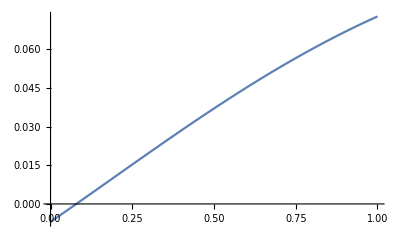

```mathematica
pars={th->0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,p->0.9,γ->1,η->1};
Plot[s/.pars/.m->0.6/. NSolve[(F[xm,n,nr]/.monopop/.pars/.m->0.6)==n,n]//Simplify,{y,0,1}]
```

```mathematica
pars={th -> 0.1,rb->10,Cc->0.1,Bb->2,Pp->0.3,γ->1,η->1,m->0.5,p->0.3};
s/.pars//Simplify
```

(n (-26.2-69.894 y-1.1 n^3 y-47.7128 y^2-1.43368 y^3+0.03013 y^4-0.000125 y^5+n^2 (17.4667-1.36667 y-2.882 y^2+0.022 y^3)+n (-8.73333-7.45733 y+7.467 y^2+2.77523 y^3-0.04323 y^4+0.000165 y^5)))/((0.333333+1. n) (1.+n+1.31 y-0.01 y^2)^2 (-1.5+n^2-3.93 y-2.54415 y^2+0.0393 y^3-0.00015 y^4+n (2.+2.62 y-0.02 y^2)))

```mathematica
NSolve[(s/.pars/.DeleteCases[Flatten[NSolve[(F[xm,n,nr]/.monopop/.pars//Simplify)==n,n]],n->0.]//Simplify)==0,y,Reals]
```

{{y→-1.41255},{y→-0.766256},{y→0.729621},{y→129.203},{y→134.342}}

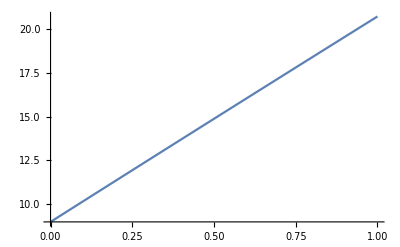

```mathematica
Plot[n/.DeleteCases[Flatten[NSolve[(F[xm,n,nr]/.monopop/.pars//Simplify)==n,n]],n->0.]//Simplify,{y,0,1}]
```

```mathematica
pars={th-> 0.1,rb-> 10,Cc-> 0.1,Bb-> 2,Pp-> 0.3,p-> 0.2,γ-> 1,η-> 1};
rates=Range[0.1,0.9,0.1];
res=Table[FindRoot[{(F[xm,n,nr]/.monopop/.pars/.m->rates[[i]])==n,(s/.pars/.m->rates[[i]]//Simplify)==0},{{n,15,1,30},{y,0.6,0,1}}],{i,Length[rates]}]
```

{{n→18.1643,y→0.67297},{n→18.0591,y→0.665105},{n→17.9686,y→0.658344},{n→17.8919,y→0.652616},{n→17.8282,y→0.64786},{n→17.7769,y→0.64403},{n→17.7375,y→0.641088},{n→17.7096,y→0.639007},{n→17.693,y→0.637765}}

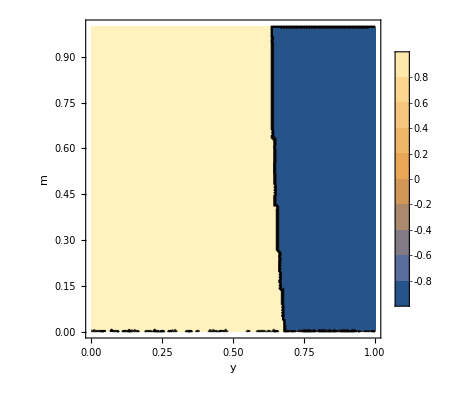

```mathematica
ContourPlot[Sign[s/.pars/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars,n]],n->0.]],{y,0,1},{m,0,1},PlotLegends-> Automatic,Frame->True,FrameLabel->{Style["y",20],Style["m",20],Style["selection gradient",20]},ImageSize->400]
```

```mathematica
Export["/home/claire/institution-evolution-new-model/analyticalpredictions.txt",TableForm[Transpose[{rates,y/.res,n/.res}]],"CSV"]
```

/home/claire/institution-evolution-new-model/analyticalpredictions.txt

### Parameters to test in simulations

```mathematica
s=((1-m) (-1+m) n^4 rb^2 (n (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+Bb (-n (-1+p) y)^γ (-2+γ)) (C1 n y+2 C2 n y^2-n Pp y (p y)^η-Bb (-n (-1+p) y)^γ γ+n Pp (p y)^η η-n Pp y (p y)^η η))/((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^4 (1-((-1+m)^2 rb (Bb^2 rb th (-n (-1+p) y)^(2 γ)-2 Bb n rb th (-n (-1+p) y)^γ (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+n^2 (rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2+Bb (-n (-1+p) y)^γ (-1+γ))))/(n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2))-(n^2 rb (C1 (-1-2 m (-1+n)+m^2 (-1+n)) n y+2 C2 (-1-2 m (-1+n)+m^2 (-1+n)) n y^2+n Pp y (p y)^η-2 m n Pp y (p y)^η+m^2 n Pp y (p y)^η+2 m n^2 Pp y (p y)^η-m^2 n^2 Pp y (p y)^η+Bb (-n (-1+p) y)^γ γ-n Pp (p y)^η η+n Pp y (p y)^η η))/((-1-2 m (-1+n)+m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2);
F[xm_,n_,nr_]:=(1-m)w[xm,xm,n]n+m nr;
w[x_,xn_,n_]:=re[x,xn,n]/(1+th re[x,xn,n]);
re[x_,xn_,n_]:=rb/n(1-(x C1+x^2 C2)+Bb((x+(n-1)xn)(1-p))^γ/n-Pp(1-x)((x+(n-1)xn)/n p)^η);
monopop={x->y,xn->y,xm->y,nr->n,r->(1-m)^2/(1+(1-(1-m)^2)(n-1)),r̄->1/n+(1-1/n)r};
```

#### Some set of pars, fill as you want

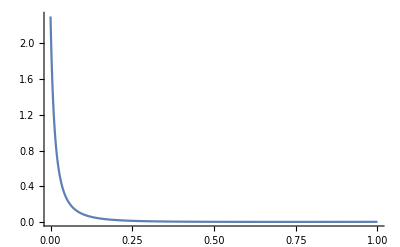

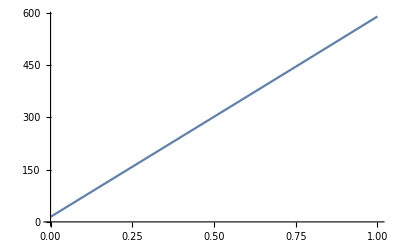

```mathematica
pars={th -> 0.1,rb-> 16,C1-> 0.1,C2-> 0,Bb-> 50,Pp-> 4.5,p-> 0.2,η-> 2,γ-> 1};
Plot[s/.pars/.m->0.2/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars,n]],n->0.],{y,0,1},PlotRange->All]
Plot[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars,n]],n->0.],{y,0,1}]
```

```mathematica
Refine[NSolve[{(n==F[xm,n,nr])/.monopop/.pars,(s==0)/.pars/.m->0.2},{n,y},Reals],{n≥0,y≥0}]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→0},{n→-561.261,y→-0.99305},{n→0,y→-0.99305}}

```mathematica
TableForm[Transpose[{rates,Table[1,Length[rates]],Table[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars1,n]],n->0.]/.y->1,Length[rates]]}]]
```

#### First set of parameters: evolution goes to 1 (pars1={th → 0.1,rb→ 10,C1→ 0.2,C2→ 0,Bb→ 6,Pp→ 0.3,p→ 0.4,η→ 1,γ→ 1})

```mathematica
pars1={th -> 0.1,rb-> 10,C1-> 0.2,C2-> 0,Bb-> 6,Pp-> 0.3,p-> 0.4,η-> 1,γ-> 1};
```

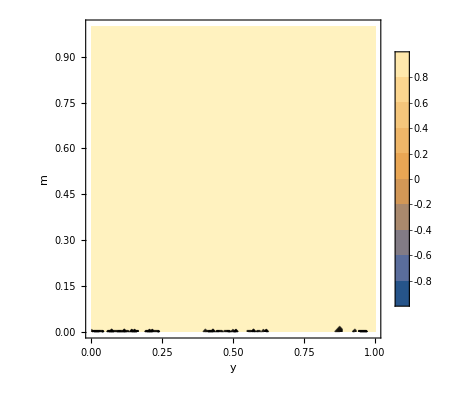

```mathematica
ContourPlot[Sign[s/.pars1/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars1,n]],n->0.]],{y,0,1},{m,0,1},PlotLegends-> Automatic,Frame->True,FrameLabel->{Style["y",20],Style["m",20],Style["selection gradient",20]},ImageSize->400]
```

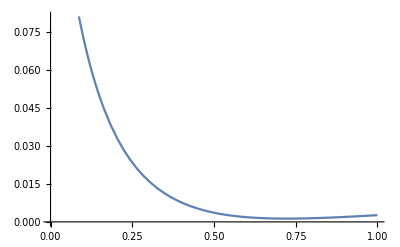

```mathematica
pars1={th -> 0.1,rb-> 10,C1-> 0.2,C2-> 0,Bb-> 6,Pp-> 0.3,p-> 0.4,η-> 1,γ-> 1};
Plot[s/.pars1/.m->0.5/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars1,n]],n->0.],{y,0,1}]
```

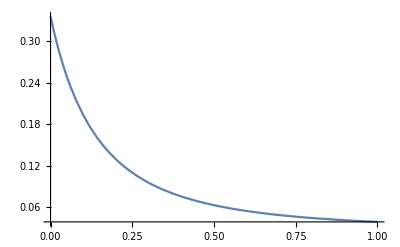

```mathematica
pars1={th -> 0.1,rb-> 10,C1-> 0.01,C2-> 0,Bb-> 6,Pp-> 0.3,p-> 0.4,η-> 1,γ-> 1};
Plot[s/.pars1/.m->0.5/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars1,n]],n->0.],{y,0,1}]
```

Selection gradient always positive: selection will favour increase of y up to 1.

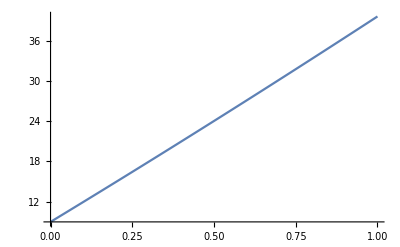

```mathematica
Plot[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars1,n]],n->0.],{y,0,1}]
```

When y=1, n=39.6

```mathematica
pred1=TableForm[Transpose[{rates,Table[1,Length[rates]],Table[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars1,n]],n->0.]/.y->1,Length[rates]]}]]
```

0.1 | 1 | 39.6
0.2 | 1 | 39.6
0.3 | 1 | 39.6
0.4 | 1 | 39.6
0.5 | 1 | 39.6
0.6 | 1 | 39.6
0.7 | 1 | 39.6
0.8 | 1 | 39.6
0.9 | 1 | 39.6

```mathematica
pred1=TableForm[{{0.1, 1, 39.6}, {0.2, 1, 39.6}, {0.30000000000000004, 1, 39.6}, {0.4, 1, 39.6}, {0.5, 1, 39.6}, {0.6, 1, 39.6}, {0.7000000000000001, 1, 39.6}, {0.8, 1, 39.6}, {0.9, 1, 39.6}}];
```

```mathematica
Export["/home/claire/institution-evolution/analyticalpredictions.txt",pred1,"CSV"]
```

/home/claire/institution-evolution/analyticalpredictions.txt

#### Second set of parameters: internal equilibrium (pars2={th→0.1,rb→20,C1→0,C2→0.1,Bb→2,Pp→0.3,p→0.5,η→1,γ→1})

```mathematica
pars2={th->0.1,rb->20,C1->0,C2->0.1,Bb->2,Pp->0.3,p->0.5,η->1,γ->1};
```

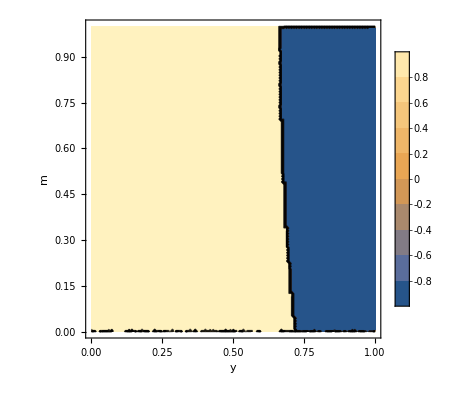

```mathematica
ContourPlot[Sign[s/.pars2/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars2,n]],n->0.]],{y,0,1},{m,0,1},PlotLegends-> Automatic,Frame->True,FrameLabel->{Style["y",20],Style["m",20],Style["selection gradient",20]},ImageSize->400]
```

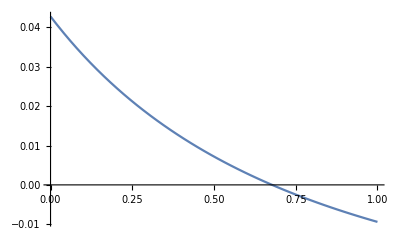

```mathematica
Plot[s/.pars2/.m->0.5/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars2,n]],n->0.],{y,0,1}]
```

Single internal attractor (stable equilibrium) within [0,1].

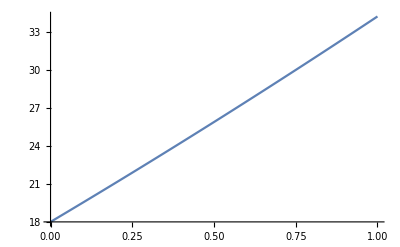

```mathematica
Plot[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars2,n]],n->0.],{y,0,1}]
```

n can be solved as a function of y.  When plugged into the selection gradient, a numerical solution for S(y)=0 can be found,  and once y* is determined, n* is easily calculated.

```mathematica
nrule=DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars2,n]],n->0.];
rates=Range[0.1,0.9,0.1];
ys=Table[DeleteCases[Flatten[NSolve[(s/.pars2/.m->rates[[i]]/.nrule)==0]],y->a_/;a<0||a>1],{i,Length[rates]}];
ns=nrule/.#&/@ys;
```

```mathematica
{y,n}/.#&/@Flatten[Transpose[{ys,ns}],{3,1}];
```

```mathematica
pred2=TableForm[Transpose[{rates,y/.ys,n/.ns}]]
```

0.1 | 0.708381 | 29.2899
0.2 | 0.698734 | 29.13
0.3 | 0.690457 | 28.993
0.4 | 0.683454 | 28.8772
0.5 | 0.677648 | 28.7813
0.6 | 0.672977 | 28.7042
0.7 | 0.669392 | 28.645
0.8 | 0.666857 | 28.6031
0.9 | 0.665346 | 28.5782

```mathematica
pred2=TableForm[{{0.1, 0.7083812144469009, 29.289856131520725}, {0.2, 0.6987340430843323, 29.130037195858765}, {0.30000000000000004, 0.6904566793614834, 28.993044577698093}, {0.4, 0.6834538591693974, 28.877242305143973}, {0.5, 0.6776480507343965, 28.78130136883398}, {0.6, 0.6729770591315059, 28.7041573146176}, {0.7000000000000001, 0.6693921934216526, 28.644977877103752}, {0.8, 0.6668568876276465, 28.603138678421782}, {0.9, 0.6653456977335019, 28.57820558306581}}];
```

```mathematica
Export["/home/claire/institution-evolution/analyticalpredictions.txt",pred2,"CSV"]
```

/home/claire/institution-evolution/analyticalpredictions.txt

#### Third set of parameters: phenotype goes to 1 and n goes to very high values (pars3={th → 0.0001,rb→10,C1→ 0.2,C2→ 0,Bb→90,Pp→ 0.9,p→ 0.4,η→ 2,γ→ 1})

```mathematica
pars3={th -> 0.0001,rb->10,C1-> 0.2,C2-> 0,Bb->90,Pp-> 0.9,p-> 0.4,η-> 2,γ-> 1};
```

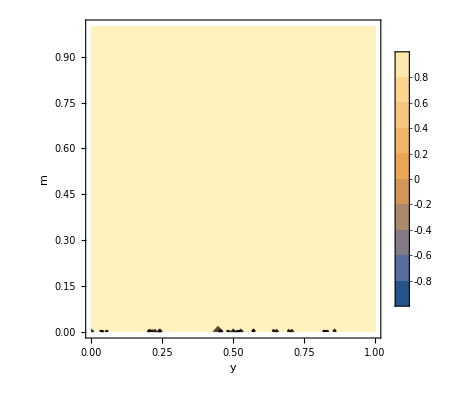

```mathematica
ContourPlot[Sign[s/.pars3/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars3,n]],n->0.]],{y,0,1},{m,0,1},PlotLegends-> Automatic,Frame->True,FrameLabel->{Style["y",20],Style["m",20],Style["selection gradient",20]},ImageSize->400]
```

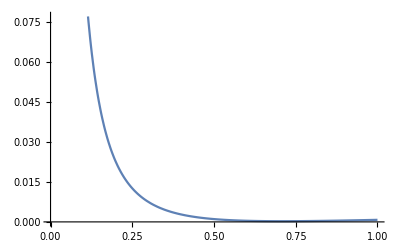

```mathematica
Plot[s/.pars3/.m->0.5/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars3,n]],n->0.],{y,0,1}]
```

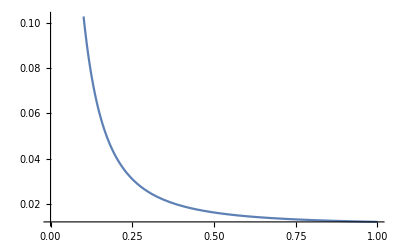

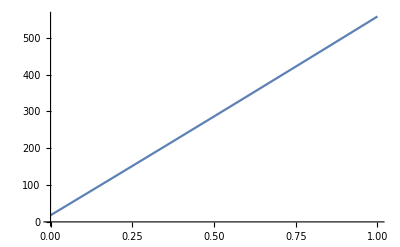

```mathematica
pars3={th -> 0.1,rb->20,C1-> 0.0001,C2-> 0,Bb->50,Pp-> 0.9,p-> 0.4,η->1,γ-> 1};
Plot[s/.pars3/.m->0.5/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars3,n]],n->0.],{y,0,1}]
Plot[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars3,n]],n->0.],{y,0,1}]
```

Selection gradient always positive: selection will favour increase of y up to 1.

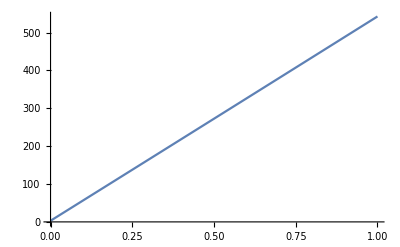

```mathematica
Plot[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars3,n]],n->0.],{y,0,1}]
```

When y→1, n→ 500

```mathematica
rates=Range[0.1,0.9,0.1];
pred1=TableForm[Transpose[{rates,Table[1,Length[rates]],Table[n/.DeleteCases[Flatten[NSolve[(n==F[xm,n,nr])/.monopop/.pars3,n]],n->0.]/.y->1,Length[rates]]}]]
```

0.1 | 1 | 547.945
0.2 | 1 | 547.945
0.3 | 1 | 547.945
0.4 | 1 | 547.945
0.5 | 1 | 547.945
0.6 | 1 | 547.945
0.7 | 1 | 547.945
0.8 | 1 | 547.945
0.9 | 1 | 547.945

```mathematica
pred1=TableForm[{{0.1, 1, 547.9452}, {0.2, 1, 547.9452}, {0.30000000000000004, 1, 547.9452}, {0.4, 1, 547.9452}, {0.5, 1, 547.9452}, {0.6, 1, 547.9452}, {0.7000000000000001, 1, 547.9452}, {0.8, 1, 547.9452}, {0.9, 1, 547.9452}}]
```

0.1 | 1 | 547.945
0.2 | 1 | 547.945
0.3 | 1 | 547.945
0.4 | 1 | 547.945
0.5 | 1 | 547.945
0.6 | 1 | 547.945
0.7 | 1 | 547.945
0.8 | 1 | 547.945
0.9 | 1 | 547.945

```mathematica
Export["/home/claire/institution-evolution/analyticalpredictions.txt",pred1,"CSV"]
```

/home/claire/institution-evolution/analyticalpredictions.txt

```mathematica
DeleteCases[Flatten[Solve[n==F[xm,n,nr]/.monopop/.{γ->1,C2->0}//Simplify,n]],n->0]
```

{n→rb (-1+th) (-1-Bb y+C1 y+Bb p y+Pp (p y)^η-Pp y (p y)^η)}

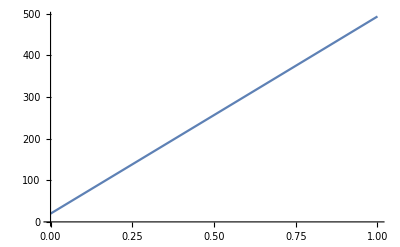

```mathematica
parameters={th -> 0.01,rb->20,C1-> 0.1,C2-> 0,Bb-> 40,Pp-> 0.3,p-> 0.4,η-> 2,γ-> 1};
Plot[rb (-1+th) (-1-Bb y+C1 y+Bb p y+Pp (p y)^η-Pp y (p y)^η)/.parameters,{y,0,1}]
```